```mathematica
<<KerrGeodesics`
```

```mathematica
$UserBaseDirectory<>$PathnameSeparator<>"Applications"
```

/Users/hoppese/Library/Mathematica/Applications

```mathematica
Quit[]
```

```mathematica
?KerrGeoOrbit
```

```mathematica
{aN,pN,eN,thMinN}={0.1`25,10,0.7`25,0.5`25}
```

{0.1,10,0.7,0.5}

```mathematica
lambdaR=2π/(KerrGeoFrequencies[aN,pN,eN,Cos[π/2+thMinN],Time->"Mino"][[1]])
lambdaTh=2π/(KerrGeoFrequencies[aN,pN,eN,Cos[π/2+thMinN],Time->"Mino"][[3]])
```

2.6358441055163382325

-1.6047021240803377

```mathematica
orbit=KerrGeoOrbit[aN,pN,eN,Cos[π/2+thMinN]];
{t,r,θ,φ}=orbit["Trajectory"];
```

```mathematica
tNs=Table[{laN,t[laN]},{laN,0,lambdaR,lambdaR/50}]
rNs=Table[{laN,r[laN]},{laN,0,lambdaR,lambdaR/50}]
thNs=Table[{laN,θ[laN]},{laN,0,lambdaTh,lambdaTh/50}]
phNs=Table[{laN,φ[laN]},{laN,0,lambdaR,lambdaR/50}]
```

{{0,0},{0.052716882110326764649,2.706552328008639},{0.1054337642206535293,5.430534939552358},{0.15815064633098029395,8.190110210152709},{0.2108675284413070586,11.00495852433629},{0.26358441055163382325,13.89717862633056},{0.3163012926619605879,16.89237767154455},{0.36901817477228735255,20.02105119541044},{0.42173505688261411719,23.32039271157415},{0.47445193899294088184,26.83673367636439},{0.52716882110326764649,30.62890822950283},{0.57988570321359441114,34.77298075576405},{0.63260258532392117579,39.36899406621547},{0.68531946743424794044,44.550729180935548},{0.73803634954457470509,50.499960964184484},{0.79075323165490146974,57.467385103203101},{0.84347011376522823439,65.803240476881169},{0.89618699587555499904,76.001322172907875},{0.94890387798588176369,88.759360539693552},{1.0016207600962085283,105.05315560649182},{1.054337642206535293,126.20313924883076},{1.1070545243168620576,153.86546210557337},{1.1597714064271888223,189.79588381654593},{1.2124882885375155869,235.16900779171386},{1.2652051706478423516,289.41546984776276},{1.3179220527581691162,349.22989041519585},{1.3706389348684958809,409.04437808084923},{1.4233558169788226455,463.29102999337496},{1.4760726990891494102,508.66443421868064},{1.5287895811994761748,544.59517879982608},{1.5815064633098029395,572.25781210819714},{1.6342233454201297041,593.40804086238138},{1.6869402275304564688,609.70197391844342},{1.7396571096407832334,622.46001962978566},{1.7923739917511099981,632.65797677368544},{1.8450908738614367627,640.99359693013105},{1.8978077559717635274,647.96071528290842},{1.950524638082090292,653.90962283681882},{2.0032415201924170567,659.09107054932997},{2.0559584023027438213,663.68688227749071},{2.108675284413070586,667.830873404843},{2.1613921665233973506,671.62310061846351},{2.2141090486337241153,675.139619326132},{2.2668259307440508799,678.43923336795047},{2.3195428128543776446,681.56822774336516},{2.3722596949647044092,684.56374127150611},{2.4249765770750311739,687.45621587932794},{2.4776934591853579385,690.27121533807624},{2.5304103412956847032,693.03081262734545},{2.5831272234060114678,695.75468437829021}}

{{0,5.882352941176470588235294},{0.052716882110326764649,5.895094323185001012},{0.1054337642206535293,5.933674870347489469},{0.15815064633098029395,5.999181199252772795},{0.2108675284413070586,6.093483712359776325},{0.26358441055163382325,6.219330438247127569},{0.3163012926619605879,6.380488400678315005},{0.36901817477228735255,6.581943540846024897},{0.42173505688261411719,6.83017485082496197},{0.47445193899294088184,7.13352405927251798},{0.52716882110326764649,7.50268887801419784},{0.57988570321359441114,7.95137472159740349},{0.63260258532392117579,8.49714449838153747},{0.68531946743424794044,9.16250208961184753},{0.73803634954457470509,9.97621701378441736},{0.79075323165490146974,10.9748104319812636},{0.84347011376522823439,12.2039002240132018},{0.89618699587555499904,13.7185910326675944},{0.94890387798588176369,15.5810115392965359},{1.0016207600962085283,17.851040943352896},{1.054337642206535293,20.5630613238361905},{1.1070545243168620576,23.6788760538514867},{1.1597714064271888223,27.0123168455611784},{1.2124882885375155869,30.15162446769465},{1.2652051706478423516,32.4692149252071645},{1.3179220527581691162,33.3333333333333333333333},{1.3706389348684958809,32.4692149252071645},{1.4233558169788226455,30.15162446769465},{1.4760726990891494102,27.0123168455611784},{1.5287895811994761748,23.6788760538514867},{1.5815064633098029395,20.5630613238361905},{1.6342233454201297041,17.851040943352896},{1.6869402275304564688,15.5810115392965359},{1.7396571096407832334,13.7185910326675944},{1.7923739917511099981,12.2039002240132018},{1.8450908738614367627,10.9748104319812636},{1.8978077559717635274,9.97621701378441736},{1.950524638082090292,9.16250208961184753},{2.0032415201924170567,8.49714449838153747},{2.0559584023027438213,7.95137472159740349},{2.108675284413070586,7.50268887801419784},{2.1613921665233973506,7.13352405927251798},{2.2141090486337241153,6.83017485082496197},{2.2668259307440508799,6.5819435408460249},{2.3195428128543776446,6.380488400678315005},{2.3722596949647044092,6.219330438247127569},{2.4249765770750311739,6.093483712359776325},{2.4776934591853579385,5.999181199252772795},{2.5304103412956847032,5.933674870347489469},{2.5831272234060114678,5.895094323185001012}}

{{0,0.5},{-0.032094042481606755,0.5144562053633826},{-0.06418808496321351,0.5555577462800667},{-0.096282127444820265,0.6179708365724479},{-0.12837616992642702,0.6959242800025675},{-0.16047021240803377,0.7847215262440601},{-0.19256425488964053,0.8809939464836376},{-0.22465829737124728,0.9824334455068986},{-0.25675233985285404,1.08746328074671},{-0.28884638233446079,1.194983724845189},{-0.32094042481606755,1.3041993411184909},{-0.3530344672976743,1.414505276075683},{-0.38512850977928106,1.5254109539628533},{-0.41722255226088781,1.6364856174187071},{-0.44931659474249457,1.7473149546400551},{-0.48141063722410132,1.8574607190818609},{-0.51350467970570808,1.966415985343051},{-0.54559872218731483,2.073547611456925},{-0.57769276466892159,2.178014431101234},{-0.60978680715052834,2.278644536353462},{-0.6418808496321351,2.373749108599243},{-0.67397489211374185,2.460852009306443},{-0.70606893459534861,2.536355109738707},{-0.73816297707695536,2.595319252386749},{-0.77025701955856212,2.631893962443388},{-0.80235106204016887,2.6411025344255239},{-0.83444510452177563,2.621479403390686},{-0.86653914700338238,2.576037432603774},{-0.89863318948498914,2.510372324449845},{-0.93072723196659589,2.430125919201777},{-0.96282127444820265,2.33974608055866},{-0.9949153169298094,2.242382058701839},{-1.0270093594114162,2.14018520035497},{-1.0591034018930229,2.034628661953786},{-1.0911974443746297,1.926745696101404},{-1.1232914868562364,1.817289752412902},{-1.1553855293378432,1.706839905885723},{-1.1874795718194499,1.595872175237712},{-1.2195736143010567,1.484811257650557},{-1.2516676567826634,1.374072795816659},{-1.2837616992642702,1.264103999432174},{-1.315855741745877,1.155430037161679},{-1.3479497842274837,1.048715030362408},{-1.3800438267090905,0.9448499156000622},{-1.4121378691906972,0.8450849388784143},{-1.444231911672304,0.7512300505060542},{-1.4763259541539107,0.6659410195259033},{-1.5084199966355175,0.5930542177577711},{-1.5405140391171242,0.5377394858933154},{-1.572608081598731,0.5058662668274662},{-1.6047021240803377,0.5019575872348271}}

{{0,0},{0.052716882110326764649,-0.411873861243736},{0.1054337642206535293,-0.739008493338841},{0.15815064633098029395,-0.975119217350875},{0.2108675284413070586,-1.148263583930446},{0.26358441055163382325,-1.28316172312601},{0.3163012926619605879,-1.396030153885196},{0.36901817477228735255,-1.497466951434713},{0.42173505688261411719,-1.595221005811929},{0.47445193899294088184,-1.696136949134922},{0.52716882110326764649,-1.807778587597013},{0.57988570321359441114,-1.940310911813875},{0.63260258532392117579,-2.10916938928885},{0.68531946743424794044,-2.338094140377485},{0.73803634954457470509,-2.655765590306084},{0.79075323165490146974,-3.062677435390504},{0.84347011376522823439,-3.481476437969127},{0.89618699587555499904,-3.821093760611488},{0.94890387798588176369,-4.067681568395662},{1.0016207600962085283,-4.248192515960056},{1.054337642206535293,-4.388250591786785},{1.1070545243168620576,-4.504852550028192},{1.1597714064271888223,-4.609024941647535},{1.2124882885375155869,-4.708690469635668},{1.2652051706478423516,-4.810682964794339},{1.3179220527581691162,-4.9223781562835},{1.3706389348684958809,-5.05351994936875},{1.4233558169788226455,-5.218789235827103},{1.4760726990891494102,-5.440923174847654},{1.5287895811994761748,-5.748852224946541},{1.5815064633098029395,-6.149066023454699},{1.6342233454201297041,-6.572466717194212},{1.6869402275304564688,-6.922992985726974},{1.7396571096407832334,-7.178601689810762},{1.7923739917511099981,-7.364663146304734},{1.8450908738614367627,-7.507683582652333},{1.8978077559717635274,-7.625516500832268},{1.950524638082090292,-7.729693141863636},{2.0032415201924170567,-7.828378592809531},{2.0559584023027438213,-7.928462411275259},{2.108675284413070586,-8.037202767365013},{2.1613921665233973506,-8.164002968552891},{2.2141090486337241153,-8.322880031774168},{2.2668259307440508799,-8.53561718437024},{2.3195428128543776446,-8.831133259150798},{2.3722596949647044092,-9.221155344165335},{2.4249765770750311739,-9.645482549057842},{2.4776934591853579385,-10.00459635964826},{2.5304103412956847032,-10.2677577261513},{2.5831272234060114678,-10.45820779330912}}

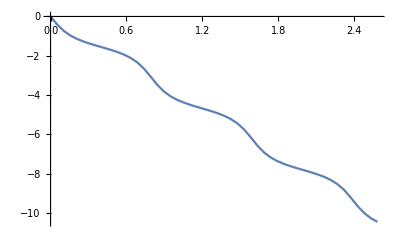

```mathematica
ListLinePlot[phNs]
```

```mathematica
?KerrGeoFrequencies
```

```mathematica
?KerrGeoConstantsOfMotion
```

```mathematica
KerrGeoConstantsOfMotion[0.1`25,10,0.7`25,Cos[π/2+0.5`25]]
```

<|ℰ→0.97628991198649760206263,ℒ→-1.89099630519393907542,𝒬→11.981965954761512355|>

```mathematica
KerrGeoFrequencies[0.1`25,10,0.7`25,Cos[π/2+0.5`25]]
KerrGeoFrequencies[0.1`25,10,0.7`25,Cos[π/2+0.5`25],Time->"Mino"]
```

<|Ω_r→0.0089957623873380733,Ω_θ→0.014885086581418986,Ω_ϕ→-0.014776217285111262|>

<|Υ_r→2.3837469348168323475,Υ_θ→3.944332674113704992,Υ_ϕ→-3.9154838850733803,Γ→264.98553787637386|>

```mathematica
2π/(KerrGeoFrequencies[0.1`25,10,0.7`25,Cos[π/2+0.5`25],Time->"Mino"][[2]])
```

-1.89099630519393907542

2.08586105455518127241

3.276439227033901729

-3.944304196508646346

1.5929653572112610205